A skyrmion

n={Cos[π/6-ArcTan[u,v]] Sin[2 ArcTan[√(u^2+v^2)]],-Sin[2 ArcTan[√(u^2+v^2)]] Sin[π/6-ArcTan[u,v]],Cos[2 ArcTan[√(u^2+v^2)]]}

|n|=1

H=4 π

Q=1

-Graphics3D-

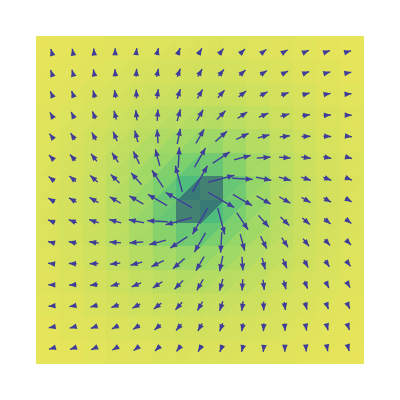

-Graphics3D-

```mathematica
Print["A skyrmion"]
α=2Pi/3;
b=2ArcTan[Sqrt[u^2+v^2]];
a=ArcTan[u,v]-α;
Print["n=",n={-Sin[a]Sin[b],Cos[a]Sin[b],Cos[b]}]
Print["|n|=",Dot[n,n]//Simplify]
Print["H=",
H=1/2Integrate[(Dot[D[n,u],D[n,u]]+Dot[D[n,v],D[n,v]]),{u,-Infinity,Infinity},{v,-Infinity,Infinity}]]
Print["Q=",
Q=1/(4Pi)Integrate[Dot[n,Cross[D[n,u],D[n,v]]],{u,-Infinity,Infinity},{v,-Infinity,Infinity}]]
n3=ArcCos[n[[3]]];
sc=8;
l=D[n,u].D[n,u]+D[n,v].D[n,v];
Plot3D[l,{u,-sc,sc},{v,-sc,sc},PlotRange->{{-sc,sc},{-sc,sc},{0,15}},Mesh->None,Boxed->False,Axes->False]
VectorDensityPlot[{Take[n,2],ArcCos[n[[3]]]},{u,-sc,sc},{v,-sc,sc},ColorFunction->"BlueGreenYellow",Frame->False]
VectorPlot3D[n,{u,-sc,sc},{v,-sc,sc},{w,-1,1},BoxRatios->{1,1,1/sc},RegionFunction->Function[{u,v,w},-0.05<w<0.0000004], VectorPoints->30,VectorStyle->"Arrow3D",VectorScale->0.05,Boxed->False,Axes->False,ImageSize->{90,50},VectorColorFunction->Function[{u,v,w,n1,n2,n3},ColorData["Rainbow"][n3]]]
```

A helix

n={0,-Sin[u],Cos[u]}

|n|=1

Volume=L^2

H=2 L^2

Volume=∞^2

H=∞

Q=0

-Graphics3D-

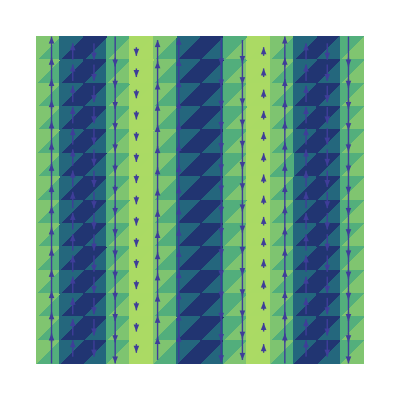

-Graphics3D-

```mathematica
Print["A helix"]
k1={1,0,0};
z={0,0,1};
r={u,v,0};
Print["n=",n=z Cos[Dot[k1,r]]+Cross[k1,z]Sin[Dot[k1,r]]]
Print["|n|=",Dot[n,n]//Simplify]
Print["Volume=",vol=L,"^2"]
Print["H=",
H=1/2Integrate[(Dot[D[n,u],D[n,u]]+Dot[D[n,v],D[n,v]]),{u,-vol,vol},{v,-vol,vol}]]
Print["Volume=",vol=Infinity,"^2"]
Print["H=",
H=1/2Integrate[(Dot[D[n,u],D[n,u]]+Dot[D[n,v],D[n,v]]),{u,-vol,vol},{v,-vol,vol}]]
Print["Q=",
Q=1/(4Pi)Integrate[Dot[n,Cross[D[n,u],D[n,v]]],{u,-vol,vol},{v,-vol,vol}]]
n3=ArcCos[n[[3]]];
sc=8;
l=D[n,u].D[n,u]+D[n,v].D[n,v];
Plot3D[l,{u,-sc,sc},{v,-sc,sc},PlotRange->{{-sc,sc},{-sc,sc},{0,15}},Mesh->None,Boxed->False,Axes->False]
VectorDensityPlot[{Take[n,2],ArcCos[n[[3]]]},{u,-sc,sc},{v,-sc,sc},ColorFunction->"BlueGreenYellow",Frame->False]
VectorPlot3D[n,{u,-sc,sc},{v,-sc,sc},{w,-1,1},BoxRatios->{1,1,1/sc},RegionFunction->Function[{u,v,w},-0.05<w<0.0000004], VectorPoints->30,VectorStyle->"Arrow3D",VectorScale->0.05,Boxed->False,Axes->False,ImageSize->{90,50},VectorColorFunction->Function[{u,v,w,n1,n2,n3},ColorData["Rainbow"][n3]]]
```

Two helices

n={Sin[v],-Sin[u],Cos[u]+Cos[v]}

|n|=2+2 Cos[u] Cos[v]

Volume=L^2

H=4 L^2

Q=(2 L Sin[L])/π

Volume=∞^2

H=∞

-Graphics3D-

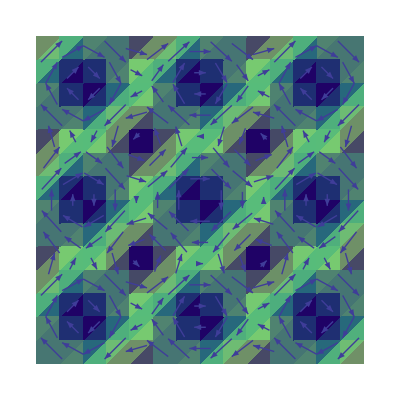

-Graphics3D-

```mathematica
Print["Two helices"]
k1={1,0,0};
k4={0,1,0};
z={0,0,1};
r={u,v,0};
Print["n=",n=z Cos[Dot[k1,r]]+Cross[k1,z]Sin[Dot[k1,r]]+z Cos[Dot[k4,r]]+Cross[k4,z]Sin[Dot[k4,r]]]
Print["|n|=",Dot[n,n]//Simplify]
Print["Volume=",vol=L,"^2"]
Print["H=",
H=1/2Integrate[(Dot[D[n,u],D[n,u]]+Dot[D[n,v],D[n,v]]),{u,-vol,vol},{v,-vol,vol}]]
Print["Q=",
Q=1/(4Pi)Integrate[Dot[n,Cross[D[n,u],D[n,v]]],{u,-vol,vol},{v,-vol,vol}]]
Print["Volume=",vol=Infinity,"^2"]
Print["H=",
H=1/2Integrate[(Dot[D[n,u],D[n,u]]+Dot[D[n,v],D[n,v]]),{u,-vol,vol},{v,-vol,vol}]]
n3=ArcCos[n[[3]]];
sc=8;
l=D[n,u].D[n,u]+D[n,v].D[n,v];
Plot3D[l,{u,-sc,sc},{v,-sc,sc},PlotRange->{{-sc,sc},{-sc,sc},{0,15}},Mesh->None,Boxed->False,Axes->False]
VectorDensityPlot[{Take[n,2],ArcCos[n[[3]]]},{u,-sc,sc},{v,-sc,sc},ColorFunction->"BlueGreenYellow",Frame->False]
VectorPlot3D[n,{u,-sc,sc},{v,-sc,sc},{w,-1,1},BoxRatios->{1,1,1/sc},RegionFunction->Function[{u,v,w},-0.05<w<0.0000004], VectorPoints->30,VectorStyle->"Arrow3D",VectorScale->0.05,Boxed->False,Axes->False,ImageSize->{90,50},VectorColorFunction->Function[{u,v,w,n1,n2,n3},ColorData["Rainbow"][n3]]]
```

Three helices

n={-1/2 √3 Sin[u/2-(√3 v)/2]+1/2 √3 Sin[u/2+(√3 v)/2],-Sin[u]-1/2 Sin[u/2-(√3 v)/2]-1/2 Sin[u/2+(√3 v)/2],Cos[u]+Cos[u/2-(√3 v)/2]+Cos[u/2+(√3 v)/2]}

|n|=1/2 (6+3 Cos[u]+8 Cos[u/2]^3 Cos[(√3 v)/2]+Cos[√3 v])

Volume=L^2

H=1/2 (12 L^2+3 L Sin[L]+8 √3 Sin[L/2] Sin[(√3 L)/2]-(8 Sin[(3 L)/2] Sin[(√3 L)/2])/(3 √3)-(L Sin[√3 L])/(√3))

Q=(3/4 L (9 L+(8+Cos[L]) Sin[L])+16 √3 Sin[L/2] Sin[(√3 L)/2]+1/2 √3 Sin[L] Sin[√3 L])/(4 π)=in large L limit=(((27 L^2)/2+O[1/L]^1)+Cos[L] ((3 L)/2+O[1/L]^2) Sin[L]+(12 L+O[1/L]^2) Sin[L]+32 √3 Sin[L/2] Sin[(√3 L)/2]+√3 Sin[L] Sin[√3 L])/(8 π)

Volume=∞^2

Integrate::idiv: Integral of 3 + 3\ Cos[u]/4 + 9/4\ Cos[u/2]\ Cos[√3\ v/2] - 1/2\ Cos[u/2]^3\ Cos[√3\ v/2] - 3/4\ Cos[u/2]\ Cos[u]\ Cos[√3\ v/2] - 1/4\ Cos[√3\ v] does not converge on {-∞, ∞}.

H=1/2 ∫_(-∞)^∞ ∫_(-∞)^∞ ((-Cos[u]-1/4 Cos[u/2-(√3 v)/2]-1/4 Cos[u/2+(√3 v)/2])^2+(3/4 Cos[u/2-(√3 v)/2]+3/4 Cos[u/2+(√3 v)/2])^2+(1/4 √3 Cos[u/2-(√3 v)/2]-1/4 √3 Cos[u/2+(√3 v)/2])^2+(-1/4 √3 Cos[u/2-(√3 v)/2]+1/4 √3 Cos[u/2+(√3 v)/2])^2+(-Sin[u]-1/2 Sin[u/2-(√3 v)/2]-1/2 Sin[u/2+(√3 v)/2])^2+(1/2 √3 Sin[u/2-(√3 v)/2]-1/2 √3 Sin[u/2+(√3 v)/2])^2)ⅆvⅆu

-Graphics3D-

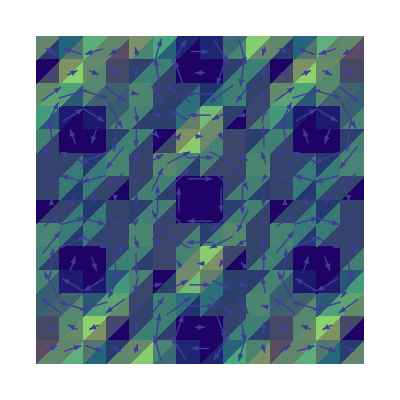

-Graphics3D-

```mathematica
Print["Three helices"]
k1={1,0,0};
k2={-1/2,Sqrt[3]/2,0};
k3={-1/2,-Sqrt[3]/2,0};
z={0,0,1};
r={u,v,0};
Print["n=",n=z Cos[Dot[k1,r]]+Cross[k1,z]Sin[Dot[k1,r]]+z Cos[Dot[k2,r]]+Cross[k2,z]Sin[Dot[k2,r]]+z Cos[Dot[k3,r]]+Cross[k3,z]Sin[Dot[k3,r]]]
Print["|n|=",Dot[n,n]//Simplify]
Print["Volume=",vol=L,"^2"]
Print["H=",
H=1/2Integrate[(Dot[D[n,u],D[n,u]]+Dot[D[n,v],D[n,v]]),{u,-vol,vol},{v,-vol,vol}]]
Print["Q=",
Q=1/(4Pi)Integrate[Dot[n,Cross[D[n,u],D[n,v]]],{u,-vol,vol},{v,-vol,vol}],"=in large L limit=",Series[Q,{L,Infinity,1}]]
Print["Volume=",vol=Infinity,"^2"]
Print["H=",
H=1/2Integrate[(Dot[D[n,u],D[n,u]]+Dot[D[n,v],D[n,v]]),{u,-vol,vol},{v,-vol,vol}]]
n3=ArcCos[n[[3]]];
sc=8;
l=D[n,u].D[n,u]+D[n,v].D[n,v];
Plot3D[l,{u,-sc,sc},{v,-sc,sc},PlotRange->{{-sc,sc},{-sc,sc},{0,15}},Mesh->None,Boxed->False,Axes->False]
VectorDensityPlot[{Take[n,2],ArcCos[n[[3]]]},{u,-sc,sc},{v,-sc,sc},ColorFunction->"BlueGreenYellow",Frame->False]
VectorPlot3D[n,{u,-sc,sc},{v,-sc,sc},{w,-1,1},BoxRatios->{1,1,1/sc},RegionFunction->Function[{u,v,w},-0.05<w<0.0000004], VectorPoints->30,VectorStyle->"Arrow3D",VectorScale->0.05,Boxed->False,Axes->False,ImageSize->{90,50},VectorColorFunction->Function[{u,v,w,n1,n2,n3},ColorData["Rainbow"][n3]]]
```

Another two helices

n={Cos[u] Sin[v],Sin[u],Cos[u] Cos[v]}

|n|=1

Volume=L^2

H=1/2 L (6 L+Sin[2 L])

Q=-(L Sin[L])/π

Volume=∞^2

H=∞

-Graphics3D-

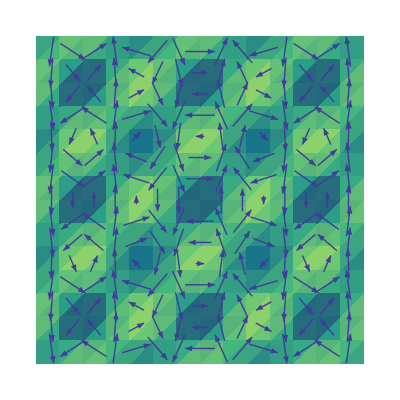

-Graphics3D-

```mathematica
Print["Another two helices"]
n0={0,0,1};
R1={{1,0,0},{0,Cos[u],Sin[u]},{0,-Sin[u],Cos[u]}};
R2={{Cos[v],0,Sin[v]},{0,1,0},{-Sin[v],0,Cos[v]}};
Print["n=",n=Dot[R2,R1,n0]]
Print["|n|=",Dot[n,n]//Simplify]
Print["Volume=",vol=L,"^2"]
Print["H=",
H=1/2Integrate[(Dot[D[n,u],D[n,u]]+Dot[D[n,v],D[n,v]]),{u,-vol,vol},{v,-vol,vol}]]
Print["Q=",
Q=1/(4Pi)Integrate[Dot[n,Cross[D[n,u],D[n,v]]],{u,-vol,vol},{v,-vol,vol}]]
Print["Volume=",vol=Infinity,"^2"]
Print["H=",
H=1/2Integrate[(Dot[D[n,u],D[n,u]]+Dot[D[n,v],D[n,v]]),{u,-vol,vol},{v,-vol,vol}]]
n3=ArcCos[n[[3]]];
sc=8;
l=D[n,u].D[n,u]+D[n,v].D[n,v];
Plot3D[l,{u,-sc,sc},{v,-sc,sc},PlotRange->{{-sc,sc},{-sc,sc},{0,15}},Mesh->None,Boxed->False,Axes->False]
VectorDensityPlot[{Take[n,2],ArcCos[n[[3]]]},{u,-sc,sc},{v,-sc,sc},ColorFunction->"BlueGreenYellow",Frame->False]
VectorPlot3D[n,{u,-sc,sc},{v,-sc,sc},{w,-1,1},BoxRatios->{1,1,1/sc},RegionFunction->Function[{u,v,w},-0.05<w<0.0000004], VectorPoints->30,VectorStyle->"Arrow3D",VectorScale->0.05,Boxed->False,Axes->False,ImageSize->{90,50},VectorColorFunction->Function[{u,v,w,n1,n2,n3},ColorData["Rainbow"][n3]]]
```